### Start choosing the example:

```mathematica
t=28;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

DataToEquations: Critical case ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

EqEliminatorX: Reached a solution!

DataToEquations: Done.

{0.056533,Null}

<|j682→0,j683→3/2,j684→2-3/2,j685→2-3/2,j686→2,j687→3/2,j688→0,j689→0,j690→0,j691→0,jt692→3/2,jt693→0,jt694→0,jt695→0,jt696→0,jt697→0,jt698→3/2,jt699→2-3/2,jt700→2-3/2,jt701→0,u702→4,u703→4,u704→11/2,u705→5,u706→11/2,u707→3/2+4,u708→4,u709→-2+3/2+11/2,u710→5,u711→11/2|>

#### Non-linear case

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

DataToEquations: Critical case ...

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

EqEliminatorX: Reached a solution!

DataToEquations: Done.

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

Step: nonlinear: -j720-u735+u740==0&&2-j720-u737+u742==0

EqEliminatorX: Reached a solution!

<|j719→2,u741→4,u743→5,j715→0,j716→3/2,j717→2-3/2,j718→2-3/2,j721→0,j722→0,j723→0,j724→0,jt725→3/2,jt726→0,jt727→0,jt728→0,jt729→0,jt730→0,jt731→3/2,jt732→2-3/2,jt733→2-3/2,jt734→0,u736→4,u738→5,u744→11/2,u740→3/2+4,u742→-2+3/2+11/2,j720→3/2,u735→4,u737→11/2,u739→11/2|>

```mathematica
v1=Values[nsol1//KeySort];
```

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)];
```

Step: nonlinear: -j720-u735+u740==0&&2-j720-u737+u742==0

System Heads: {NonNegative,Equal,Or}

Rules association input: <|j719→2,u741→4,u743→5,j715→0,j716→j720,j717→2-j720,j718→2-j720,j721→0,j722→0,j723→0,j724→0,jt725→j720,jt726→0,jt727→0,jt728→0,jt729→0,jt730→0,jt731→j720,jt732→2-j720,jt733→2-j720,jt734→0,u736→4,u738→5,u744→u739|>

NonNegative: NonNegative[j720]&&NonNegative[2-j720]&&NonNegative[2-j720]&&NonNegative[j720]&&NonNegative[j720]&&NonNegative[j720]&&NonNegative[2-j720]&&NonNegative[2-j720]&&NonNegative[4-u735]&&NonNegative[-u737+u740]&&NonNegative[-u739+u740]&&NonNegative[u737-u740]&&NonNegative[u737-u739]&&NonNegative[5-u742]

Alternatives: (j720==0||-4+u735==0)&&(j720==0||u739-u740==0)&&(2-j720==0||-u737+u739==0)&&(2-j720==0||-5+u742==0)

Equalities: -j720-u735+u740==0&&2-j720-u737+u742==0

<|j719→2,u741→4,u743→5,j715→0,j716→j720,j717→2-j720,j718→2-j720,j721→0,j722→0,j723→0,j724→0,jt725→j720,jt726→0,jt727→0,jt728→0,jt729→0,jt730→0,jt731→j720,jt732→2-j720,jt733→2-j720,jt734→0,u736→4,u738→5,u744→u739,u740→j720+u735,u742→-2+j720+u737|>

```mathematica
v2=Values@KeySort@nsol2;
```

```mathematica
v0 //Values
v1
v2
```

{0,3/2,1/2,1/2,2,3/2,0,0,0,0,3/2,0,0,0,0,0,3/2,1/2,1/2,0,4,4,11/2,5,11/2,11/2,4,5,5,11/2}

{0,3/2,1/2,1/2,2,3/2,0,0,0,0,3/2,0,0,0,0,0,3/2,1/2,1/2,0,4,4,11/2,5,11/2,11/2,4,5,5,11/2}

{0,3/2,1/2,1/2,2,3/2,0,0,0,0,3/2,0,0,0,0,0,3/2,1/2,1/2,0,4,4,11/2,5,11/2,11/2,4,5,5,11/2}

```mathematica
(MFGEquations["Nlhs"])/.nsol
MFGEquations["Nrhs"]/.nsol
```

{17.2731,0.}

{0.,-17.2731}

```mathematica
MFGEquations["Nlhs"]/.MFGEquations["criticalreduced"][[2]]
MFGEquations["Nrhs"]/.MFGEquations["criticalreduced"][[2]]
```

{0,0}

{17.2731,0.}

```mathematica
MFGEquations["Nrhs"]
```

{-j229+Intg[-j229],2-j229+Intg[2-j229]}

```mathematica
Norm[(MFGEquations["Nrhs"]-MFGEquations["Nlhs"])/.nsol]
```

24.4279

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["criticalreduced"][[2]]]//KeySort
```

System Heads: {NonNegative,Equal,Or}

Rules association input: <|j228→2,u250→1,u252→5,j224→0,j225→j229,j226→2-j229,j227→2-j229,j230→0,j231→0,j232→0,j233→0,jt234→j229,jt235→0,jt236→0,jt237→0,jt238→0,jt239→0,jt240→j229,jt241→2-j229,jt242→2-j229,jt243→0,u245→1,u247→5,u253→u248|>

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

<|j224→0,j225→0,j226→2-0,j227→2-0,j228→2,j229→0,j230→0,j231→0,j232→0,j233→0,jt234→0,jt235→0,jt236→0,jt237→0,jt238→0,jt239→0,jt240→0,jt241→2-0,jt242→2-0,jt243→0,u244→-10.2731,u245→1,u246→7.,u247→5,u248→7.,u249→17.2731+1. 0+1. (-10.2731),u250→1,u251→-2.+1. 0+1. 7.,u252→5,u253→7.|>

### What we this plot for?

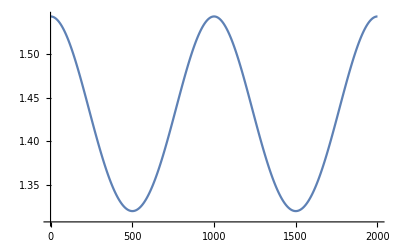

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.

### New alternative to solving the equations

```mathematica
AA=MFGEquations["EqAllAll"];
NN=Select[AA,Head[#]===NonNegative&];
OO = Select[AA,Head[#]===Or&];
EE=Select[AA,Head[#]===Equal&];
Timing[Simplify[NN];](*note the semi-colon!*)
Timing[FullSimplify[NN];]
Timing[Reduce[NN,Reals];](*Takes more time, but shows the equalities.*)
```

{0.000161,Null}

{0.000099,Null}

{0.009054,Null}

### One iteration to solve the critical congestion case:

```mathematica
rdcd=EqEliminatorX2[{MFGEquations["EqAllAll"]&&MFGEquations["EqCriticalCase"], MFGEquations["BoundaryRules"]}]
```

```mathematica
rdcd=FixedPoint[EqEliminatorX2,{MFGEquations["EqAllAll"], MFGEquations["BoundaryRules"]},10]
```

{(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0),NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46],<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>}

```mathematica
rdcd[[1]] = rdcd[[1]]&&rdcd[[2]]
```

(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0)&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46]

```mathematica
rdcd[[2]] =rdcd[[3]]
```

<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>

```mathematica
rdcd
```

{(j15==0||-2+u45==0)&&(2-j15==0||-1+u46==0)&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[j15]&&NonNegative[2-j15]&&NonNegative[2-u45]&&NonNegative[1-u46],<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>,<|j19→2,u47→2,u48→1,j14→2,j16→2-j15,j17→j15,j18→2-j15,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→j15+0,jt29→2-j15-0,jt30→-0,jt31→0,jt33→-0,jt34→j15,jt35→0,jt36→2-j15,jt37→0,u41→2,u42→1,u49→u38,jt32→0,u39→u40,u43→u38,u44→u40|>}

```mathematica
EqEliminatorX2[rdcd]
```

System Heads: Equal

Rules association input: <|j195→2,u217→1,u219→5,j191→0,j192→j196,j193→2-j196,j194→2-j196,j197→0,j198→0,j199→0,j200→0,jt201→j196,jt202→0,jt203→0,jt204→0,jt205→0,jt206→0,jt207→j196,jt208→2-j196,jt209→2-j196,jt210→0,u212→1,u214→5,u216→j196+u211,u218→-2+j196+u213,u220→u215|>

{True,True,<|j195→2,u217→1,u219→5,j191→0,j192→2,j193→2-2,j194→2-2,j197→0,j198→0,j199→0,j200→0,jt201→2,jt202→0,jt203→0,jt204→0,jt205→0,jt206→0,jt207→2,jt208→2-2,jt209→2-2,jt210→0,u212→1,u214→5,u216→2+1,u218→-2+2+3,u220→3,j196→2,u211→1,u213→3,u215→3|>}

```mathematica
m=4;rdcd2=FixedPointList[EqEliminatorX2,rdcd,m]
```

```mathematica
EqEliminatorX2[{MFGEquations["reduced"][[1]]&&MFGEquations["EqCriticalCase"], MFGEquations["reduced"][[2]]}]
```

{(u344<5&&u337==1&&j322==2&&u341==u342&&u339==u342)||(u344==5&&((u337<1&&j322==0&&u341==u342&&u339==u342)||(u337==1&&0≤j322≤2&&u341==u342&&u339==u342))),True,-j322-u337+u342==0&&2-j322-u339+u344==0,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u346→u341,u342→j322+u337,u344→-2+j322+u339|>}

```mathematica
Reduce[And @@(FullSimplify[rdcd[[2]]/.rdcd[[4]]][[#]]&/@Range[3]),Reals]
```

0≤j256≤2&&u271≤1

```mathematica
rdcd2
```

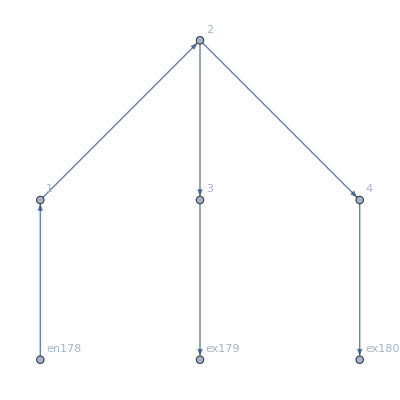
<|FG→-Graphics-,EqAllAll→NonNegative[j181]&&NonNegative[j182]&&NonNegative[j183]&&NonNegative[j184]&&NonNegative[j185]&&NonNegative[j186]&&NonNegative[j187]&&NonNegative[j188]&&NonNegative[j189]&&NonNegative[j190]&&NonNegative[j191]&&NonNegative[j192]&&NonNegative[jt193]&&NonNegative[jt194]&&NonNegative[jt195]&&NonNegative[jt196]&&NonNegative[jt197]&&NonNegative[jt198]&&NonNegative[jt199]&&NonNegative[jt200]&&NonNegative[jt201]&&NonNegative[jt202]&&NonNegative[jt203]&&NonNegative[jt204]&&j187==jt193&&j186==jt194&&j181==jt195+jt196&&j188==jt197+jt198&&j189==jt199+jt200&&j182==jt201&&j190==jt202&&j183==jt203&&j191==jt204&&j181==jt194&&j192==jt193&&j187==jt197+jt199&&j182==jt195+jt200&&j183==jt196+jt198&&j188==jt202&&j184==jt201&&j189==jt204&&j185==jt203&&j186==2&&u214==2&&u215==1&&NonNegative[u205-u216]&&NonNegative[-u206+u211]&&NonNegative[-u207+u211]&&NonNegative[u206-u211]&&NonNegative[u206-u207]&&NonNegative[u207-u211]&&NonNegative[-u206+u207]&&NonNegative[u208-u212]&&NonNegative[u209-u213]&&-u210+u216==0&&-u208+u214==0&&-u209+u215==0&&(j187==0||j181==0)&&(j188==0||j182==0)&&(j189==0||j183==0)&&(j190==0||j184==0)&&(j191==0||j185==0)&&(j192==0||j186==0)&&(jt193==0||jt194==0)&&(jt195==0||jt197==0)&&(jt196==0||jt199==0)&&(jt198==0||jt200==0)&&(jt201==0||jt202==0)&&(jt203==0||jt204==0)&&jt193==0&&(jt194==0||-u205+u216==0)&&(jt195==0||-u206+u211==0)&&(jt196==0||-u207+u211==0)&&(jt197==0||u206-u211==0)&&(jt198==0||u206-u207==0)&&(jt199==0||u207-u211==0)&&(jt200==0||-u206+u207==0)&&(jt201==0||-u208+u212==0)&&jt202==0&&(jt203==0||-u209+u213==0)&&jt204==0,BoundaryRules→{j186→2,u214→2,u215→1},reduced→{(u213<1&&u212==2&&j182==2&&u207==u211&&u206==u211&&jt199==0)||(u213==1&&((u212<2&&j182==0&&u207==u211&&u206==u211&&jt199==0)||(u212==2&&0≤j182≤2&&u207==u211&&u206==u211&&jt199==0))),<|j186→2,u214→2,u215→1,j181→2,j183→2-j182,j184→j182,j185→2-j182,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,jt193→0,jt194→2,jt195→j182+jt199,jt196→2-j182-jt199,jt197→-jt199,jt198→jt199,jt200→-jt199,jt201→j182,jt202→0,jt203→2-j182,jt204→0,u208→2,u209→1,u216→u205,u210→u205|>},Nlhs→{2-u205+u211,j182-u206+u212,2-j182-u207+u213},EqCriticalCase→2-u205+u211==0&&j182-u206+u212==0&&2-j182-u207+u213==0,criticalreduced→{True,<|j186→2,u214→2,u215→1,j181→2,j183→2-1/2,j184→1/2,j185→2-1/2,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,jt193→0,jt194→2,jt195→1/2+0,jt196→2-1/2-0,jt197→-0,jt198→0,jt200→-0,jt201→1/2,jt202→0,jt203→2-1/2,jt204→0,u208→2,u209→1,u216→9/2,u210→9/2,u211→-2+9/2,u212→-1/2+5/2,u213→-2+1/2+5/2,j182→1/2,jt199→0,u205→9/2,u206→5/2,u207→5/2|>},Nrhs→{-2.5,j182+Intg[j182],2-j182+Intg[2-j182]},EqGeneralCase→2-u205+u211==-2.5&&j182-u206+u212==j182+Intg[j182]&&2-j182-u207+u213==2-j182+Intg[2-j182]|>

```mathematica
MFGEquations
```

```mathematica
FixedSolverStepX2[MFGEquations][]
```